```mathematica
NS["det_hessian"]
```

```mathematica
wd="C:\\Users\\pglpm\\repositories\\neurobayes\\";
```

```mathematica
ClearAll[states];states[n_]:=states[n]=Tuples[{0,1},n]
```

```mathematica
ClearAll[vars];vars[n_]:=vars[n]=aboveanddiag[Table[h[i,j],{i,n},{j,n}]]
```

```mathematica
ClearAll[z];z[n_]:=z[n]=Block[{coe=mfromaboveanddiag[vars[n]]},
Sum[Exp[s.coe.s],{s,states[n]}]]
```

```mathematica
ClearAll[det];det[n_]:=det[n]=
Simplify@Det[D[Log[z[n]],{vars[n],2}]]
```

```mathematica
det[2]
```

ⅇ^(2 h[1,1]+h[1,2]+2 h[2,2])/((1+ⅇ^h[1,1]+ⅇ^h[2,2]+ⅇ^(h[1,1]+h[1,2]+h[2,2]))^4)

```mathematica
ClearAll[prodprob];prodprob[n_]:=prodprob[n]=
Block[{coe=mfromaboveanddiag[vars[n]]},
Simplify[Exp@(Sum[s.coe.s,{s,states[n]}])/(z[n]^(2^n))]]
```

```mathematica
prodprob[2]
```

ⅇ^(2 h[1,1]+h[1,2]+2 h[2,2])/((1+ⅇ^h[1,1]+ⅇ^h[2,2]+ⅇ^(h[1,1]+h[1,2]+h[2,2]))^4)

```mathematica
det[2]==prodprob[2]
```

True

```mathematica
det[1]==prodprob[1]
```

True

```mathematica
det[3]
```

(ⅇ^(3 h[1,1]+h[1,2]+h[1,3]+3 h[2,2]+h[2,3]+3 h[3,3]) (1+ⅇ^(h[1,1]+h[1,2]+h[1,3])+ⅇ^(h[1,2]+h[2,2]+h[2,3])+ⅇ^(h[1,1]+h[1,2]+h[1,3]+h[2,2]+h[2,3])+ⅇ^(h[1,3]+h[2,3]+h[3,3])+ⅇ^(h[1,1]+h[1,2]+h[1,3]+h[2,3]+h[3,3])+ⅇ^(h[1,2]+h[1,3]+h[2,2]+h[2,3]+h[3,3])+ⅇ^(h[1,1]+h[1,2]+h[1,3]+h[2,2]+h[2,3]+h[3,3])))/(1+ⅇ^h[1,1]+ⅇ^h[2,2]+ⅇ^(h[1,1]+h[1,2]+h[2,2])+ⅇ^h[3,3]+ⅇ^(h[1,1]+h[1,3]+h[3,3])+ⅇ^(h[2,2]+h[2,3]+h[3,3])+ⅇ^(h[1,1]+h[1,2]+h[1,3]+h[2,2]+h[2,3]+h[3,3]))^7

```mathematica
prodprob[3]
```

ⅇ^(2 (2 h[1,1]+h[1,2]+h[1,3]+2 h[2,2]+h[2,3]+2 h[3,3]))/(1+ⅇ^h[1,1]+ⅇ^h[2,2]+ⅇ^(h[1,1]+h[1,2]+h[2,2])+ⅇ^h[3,3]+ⅇ^(h[1,1]+h[1,3]+h[3,3])+ⅇ^(h[2,2]+h[2,3]+h[3,3])+ⅇ^(h[1,1]+h[1,2]+h[1,3]+h[2,2]+h[2,3]+h[3,3]))^8

```mathematica
prodprob[3]*z[3]^8
```

ⅇ^(2 (2 h[1,1]+h[1,2]+h[1,3]+2 h[2,2]+h[2,3]+2 h[3,3]))

```mathematica
z[3]^8
```

(1+ⅇ^h[1,1]+ⅇ^h[2,2]+ⅇ^(h[1,1]+h[1,2]+h[2,2])+ⅇ^h[3,3]+ⅇ^(h[1,1]+h[1,3]+h[3,3])+ⅇ^(h[2,2]+h[2,3]+h[3,3])+ⅇ^(h[1,1]+h[1,2]+h[1,3]+h[2,2]+h[2,3]+h[3,3]))^8

```mathematica
Map[Element[#,Reals]&,vars[2]]
```

{h[1,1]∈ℝ,h[1,2]∈ℝ,h[2,2]∈ℝ}

```mathematica
Assuming[Map[Element[#,Reals]&,vars[3]],FS[det[3]*z[3]^8]]
```

ⅇ^(3 h[1,1]+h[1,2]+h[1,3]+3 h[2,2]+h[2,3]+3 h[3,3]) (1+ⅇ^h[1,1]+ⅇ^h[2,2]+ⅇ^(h[1,1]+h[1,2]+h[2,2])+ⅇ^h[3,3]+ⅇ^(h[1,1]+h[1,3]+h[3,3])+ⅇ^(h[2,2]+h[2,3]+h[3,3]) (1+ⅇ^(h[1,1]+h[1,2]+h[1,3]))) (1+ⅇ^(h[1,1]+h[1,2]+h[1,3])+ⅇ^(h[1,2]+h[2,2]+h[2,3]) (1+ⅇ^(h[1,1]+h[1,3]))+ⅇ^(h[1,3]+h[2,3]+h[3,3]) (1+ⅇ^h[1,2] (ⅇ^h[1,1]+ⅇ^h[2,2] (1+ⅇ^h[1,1]))))

```mathematica
ClearAll[rat];rat[n_]:=rat[n]=Assuming[Map[Element[#,Reals]&,vars[n]],ExpandAll[det[n]*z[n]^(2^n)-prodprob[n]*z[n]^(2^n)]]
```

```mathematica
ClearAll[rtab];rtab[n_,samples_]:=Table[map=MapThread[Function[{x,y},x->y],{vars[n],RandomReal[{-10,10},(n^2+n)/2]}];
Log[(det[n]*z[n]^(2^n))/.map]-Log[(prodprob[n]*z[n]^(2^n))/.map],samples]//N
```

```mathematica
rtab[3,10]
```

{30.9483,15.5912,32.129,13.8611,29.6771,34.0034,15.7961,22.3649,18.0404,9.85598}

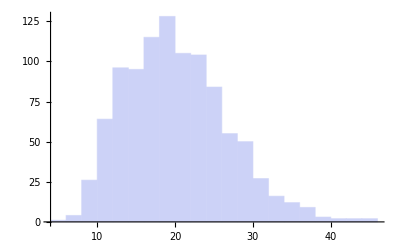

```mathematica
Histogram[rtab[3,1000],"FreedmanDiaconis",PlotRange->All]
```

```mathematica
rtab[4,10]
```

$Aborted

```mathematica
FS[prodprob[3]==det[3]]
```

$Aborted